```mathematica
(* 1.Feladat OK *)
<<VariationalMethods`
firstF[x_,y_,yd_]:=Sqrt[1+yd^2];
firstAE=FullSimplify[EulerEquations[firstF[x,y[x],y'[x]],y[x],x]]

Manipulate[
firstY = DSolveValue[{firstAE, y[a[[1]]] == a[[2]], y[b[[1]]] == b[[2]]}, y, x];
Plot[firstY[x],{x,a[[1]],b[[1]]},PlotLabel->ArcLength[Line[{{a[[1]],a[[2]]},{b[[1]],b[[2]]}}]],PlotStyle->Red,PlotRange->{{0,3},{0,4}}],
{{a,{0,0}},Locator}, {{b, {3,4}}, Locator}
]
```

y''[x]/(√(1+y'[x]^2))==0

```mathematica
(*3. Feladat*)
{x0,y0}={0,0};
{x1,y1}={2,-1};
g=9.81;

xgamma=Interpolation[{{0,0},{0.1,0.20920779025264685},{0.2,0.4173143292731987},{0.30000000000000004,0.6433438583238918},{0.4,0.8454464723174622},{0.5,1.0483595257521727},{0.6,1.2810417741293318},{0.7000000000000001,1.4324102465866777},{0.8,1.670551881612325},{0.9,1.849854247738263},{1,2}}];

ygamma=Interpolation[{{0,0},{0.1,-0.09830706451409998},{0.2,-0.18597952682698346},{0.30000000000000004,-0.2922175903934895},{0.4,-0.3758268370548955},{0.5,-0.4246485331888572},{0.6,-0.5607198627905221},{0.7000000000000001,-0.6227727433112606},{0.8,-0.7024793058085955},{0.9,-0.8655440671292081},{1,-1}}];

Manipulate[
plotPointsAB=Graphics[{
{PointSize[0.015],Point[{{x0,y0},{x1,y1}}]},
Text[Style["A(0,0)",FontSize->14],{0.2,0.1}],
Text[Style["B(2,-1)",FontSize->14],{2.1,-0.9}]
},Axes->True
,AxesStyle->Arrowheads[{0.0,0.03}]];
plotGamma=ParametricPlot[{xgamma[t],ygamma[t]},{t,0,1},PlotStyle->Purple];
Show[plotPointsAB,plotGamma],
{x0, 0, 2}, {y0, 0, 2}, {x1, 2, 4}, {y1, 0, -2}
]
```

```mathematica
(*(*2. Feladat*)

{x0,y0}={0,0};
{x1,y1}={2,-1};
g=9.81;

{bcX,bcY}=Module[{x,y,xbc,ybc,wok,cok,dok},
x[u_]:=c*w*u-c/2*Sin[2*w*u]+d;
y[u_]:=c/2-c/2*Cos[2*w*u];
{{wok,cok,dok}}={w,c,d}/.NSolve[{x[0]==x0,y[0]==y0,x[1]==x1,y[1]==y1},{c,w,d},Reals];
xbc[t_]:=x[t]/.{w->wok,c->cok,d->dok};
ybc[t_]:=y[t]/.{w->wok,c->cok,d->dok};
{xbc,ybc}
];
bcPlot=ParametricPlot[{bcX[t],bcY[t]},{t,0,1},PlotStyle->Red];

(*Join[{{0,x0}},Table[{t,2*t+RandomReal[]*0.1},{t,0.1,0.9,0.1}],{{1,x1}}]*)
xgamma=Interpolation[{{0,0},{0.1,0.20920779025264685},{0.2,0.4173143292731987},{0.30000000000000004,0.6433438583238918},{0.4,0.8454464723174622},{0.5,1.0483595257521727},{0.6,1.2810417741293318},{0.7000000000000001,1.4324102465866777},{0.8,1.670551881612325},{0.9,1.849854247738263},{1,2}}];

ygamma=Interpolation[{{0,0},{0.1,-0.09830706451409998},{0.2,-0.18597952682698346},{0.30000000000000004,-0.2922175903934895},{0.4,-0.3758268370548955},{0.5,-0.4246485331888572},{0.6,-0.5607198627905221},{0.7000000000000001,-0.6227727433112606},{0.8,-0.7024793058085955},{0.9,-0.8655440671292081},{1,-1}}];

plotPointsAB=Graphics[{
{PointSize[0.015],Point[{{x0,y0},{x1,y1}}]},
Text[Style["A(0,0)",FontSize->14],{0.2,0.1}],
Text[Style["B(2,-1)",FontSize->14],{2.1,-0.9}]
},Axes->True
,AxesStyle->Arrowheads[{0.0,0.03}]];

(*Lila gorbe*)
plotGamma=ParametricPlot[{xgamma[t],ygamma[t]},{t,0,1},PlotStyle->Purple];

pathTime[{x_,y_},umin_:0,umax_]:=
NIntegrate[Sqrt[(x'[u]^2+y'[u]^2)/(2*g*(y[umin]-y[u]))],{u,umin,umax}];
(* Idő szerinti paraméterezés. 
Visszatérít egy tp függvényt, amely megadja, hogy adott t időpillanatnak milyen u paraméter felel meg.*)
timeParametrization[{x_,y_},umin_:0,umax_]:=Module[{pf,tmax,tp},
pf=Interpolation[
Join[
{{0,umin}},
Table[{
pathTime[{x,y},umin,N[umin+(umax-umin)*i/100]],
N[umin+(umax-umin)*i/100]
},{i,100}]]];
tmax=pathTime[{x,y},umin,umax];
tp[t_]:=Piecewise[{
{umin,t≤0},
{pf[t],0<t<tmax},
{umax,t≥tmax}}];
tp
]

(*Megadva egy görbét, az idő paraméterezést, az aktuális időpontot és színt kirjazolja a megfelelő helyre a testet*)
drawBall[{x_,y_},tp_,t_,color_]:=Graphics[{color,Disk[{x[tp[t]],y[tp[t]]},0.025]}];





tpgamma=timeParametrization[{xgamma,ygamma},0,1];

Animate[
Show[
plotPointsAB,
Graphics[{
{Green,Line[{{0,0},{0,-1},{2,-1}}]},
{Blue,Line[{{0,0},{2,-1}}]}
}],
Plot[0.25(x-2)^2-1,{x,0,2},PlotStyle->Orange],
plotGamma,

drawBall[{xgamma,ygamma},tpgamma,t,Purple],

bcPlot
]
,{t,0,2},AnimationRunning->False,SaveDefinitions->True,AnimationRate->1
]*)
```

```mathematica
(*2. Feladat*)
{x0,y0}={0,0};
{x1,y1}={2,-1};
g=9.81;

plotPointsAB=Graphics[{
{PointSize[0.015],Point[{{x0,y0},{x1,y1}}]},
Text[Style["A(0,0)",FontSize->14],{0.2,0.1}],
Text[Style["B(2,-1)",FontSize->14],{2.1,-0.9}]
},Axes->True
,AxesStyle->Arrowheads[{0.0,0.03}]];

pathTime[{x_,y_},umin_:0,umax_]:=
NIntegrate[Sqrt[(x'[u]^2+y'[u]^2)/(2*g*(y[umin]-y[u]))],{u,umin,umax}];
(* Idő szerinti paraméterezés. 
Visszatérít egy tp függvényt, amely megadja, hogy adott t időpillanatnak milyen u paraméter felel meg.*)
timeParametrization[{x_,y_},umin_:0,umax_]:=Module[{pf,tmax,tp},
pf=Interpolation[
Join[
{{0,umin}},
Table[{
pathTime[{x,y},umin,N[umin+(umax-umin)*i/100]],
N[umin+(umax-umin)*i/100]
},{i,100}]]];
tmax=pathTime[{x,y},umin,umax];
tp[t_]:=Piecewise[{
{umin,t≤0},
{pf[t],0<t<tmax},
{umax,t≥tmax}}];
tp
]

(*Megadva egy görbét, az idő paraméterezést, az aktuális időpontot és színt kirjazolja a megfelelő helyre a testet*)
drawBall[{x_,y_},tp_,t_,color_]:=Graphics[{color,Disk[{x[tp[t]],y[tp[t]]},0.025]}];
```

```mathematica
(*Lila gorbe labdaval*)
lilaX=Interpolation[{{0,0},{0.1,0.20920779025264685},{0.2,0.4173143292731987},{0.30000000000000004,0.6433438583238918},{0.4,0.8454464723174622},{0.5,1.0483595257521727},{0.6,1.2810417741293318},{0.7000000000000001,1.4324102465866777},{0.8,1.670551881612325},{0.9,1.849854247738263},{1,2}}];
lilaY=Interpolation[{{0,0},{0.1,-0.09830706451409998},{0.2,-0.18597952682698346},{0.30000000000000004,-0.2922175903934895},{0.4,-0.3758268370548955},{0.5,-0.4246485331888572},{0.6,-0.5607198627905221},{0.7000000000000001,-0.6227727433112606},{0.8,-0.7024793058085955},{0.9,-0.8655440671292081},{1,-1}}];

lilaPlot=ParametricPlot[{lilaX[t],lilaY[t]},{t,0,1}, PlotStyle->Purple];
tpLila = timeParametrization[{lilaX, lilaY}, 0,1];
tmaxLila = pathTime[{lilaX,lilaY},0,1];

tmaxLila=pathTime[{lilaX,lilaY},0,1];
Animate[
Column[{
"t    :"<>ToString[t],
"t_max  :"<>ToString[tmaxLila],
Show[
plotPointsAB,
lilaPlot,
drawBall[{lilaX,lilaY},tpLila,t,Purple],
PlotLabel->"A görbe menti mozgás szimulációja ",
ImageSize->Medium
]}]
,{t,0,1},AnimationRunning->False,SaveDefinitions->True,AnimationRate->1
]
lilaHossz = ArcLength[{lilaX[t],lilaY[t]},{t,0,1}];
```

```mathematica
(*Piros gorbe labdaval*)
tpbc=timeParametrization[{bcX,bcY},0,1];
tmaxbc=pathTime[{bcX,bcY},0,1];
Animate[
Column[{
"t    :"<>ToString[t],
"t_max  :"<>ToString[tmaxbc],
Show[
plotPointsAB,
bcPlot,
drawBall[{bcX,bcY},tpbc,t,Red],
PlotLabel->"A görbe menti mozgás szimulációja ",
ImageSize->Medium
]}]
,{t,0,2},AnimationRunning->False,SaveDefinitions->True,AnimationRate->1
]
pirosHossz = ArcLength[{bcX[t],bcY[t]},{t,0,1}];
```

```mathematica
(*Narancssarga gorbe labdaval*)
narancsGorbeX[t_]:=t;
narancsGorbeY[t_]:=0.25(t-2)^2-1;
narancsPlot = ParametricPlot[{narancsGorbeX[t], narancsGorbeY[t]}, {t, 0, 2}, PlotStyle->Orange];
tpNarancs = timeParametrization[{narancsGorbeX, narancsGorbeY}, 0,2];
tmaxNarancs = pathTime[{narancsGorbeX,narancsGorbeY},0,2];

tmaxNarancs=pathTime[{narancsGorbeX,narancsGorbeY},0,2];
Animate[
Column[{
"t    :"<>ToString[t],
"t_max  :"<>ToString[tmaxNarancs],
Show[
plotPointsAB,
narancsPlot,
drawBall[{narancsGorbeX,narancsGorbeY},tpNarancs,t,Orange],
PlotLabel->"A görbe menti mozgás szimulációja ",
ImageSize->Medium
]}]
,{t,0,2},AnimationRunning->False,SaveDefinitions->True,AnimationRate->1
]
narancsHossz = ArcLength[{narancsGorbeX[t],narancsGorbeY[t]},{t,0,1}];
```

```mathematica
(*Zold gorbe labdaval*)
zoldX[t_] := Piecewise[{{0,t<1},{(t-1)*2,t≥1}}];
zoldY[t_] := Piecewise[{{-t,t<1},{-1,t≥1}}];
zoldPlot=ParametricPlot[{zoldX[t],zoldY[t]},{t,0,2}, PlotStyle->Green];
tpZold = timeParametrization[{zoldX, zoldY}, 0,2];
tmaxZold = pathTime[{zoldX,zoldY},0,2];

tmaxZold=pathTime[{zoldX,zoldY},0,2];
Animate[
Column[{
"t    :"<>ToString[t],
"t_max  :"<>ToString[tmaxZold],
Show[
plotPointsAB,
zoldPlot,
drawBall[{zoldX,zoldY},tpZold,t,Green],
PlotLabel->"A görbe menti mozgás szimulációja ",
ImageSize->Medium
]}]
,{t,0,2},AnimationRunning->False,SaveDefinitions->True,AnimationRate->1
]
zoldHossz = ArcLength[{zoldX[t],zoldY[t]},{t,0,1}];
```

```mathematica
(*Kek gorbe labdaval*)
A={0,0};
B={2,-1};
kekX[t_] := A[[1]]+t*(B[[1]]-A[[1]]);
kekY[t_] := A[[2]]+t*(B[[2]]-A[[2]]);
kekPlot=ParametricPlot[{kekX[t],kekY[t]},{t,0,1}, PlotStyle->Blue, PlotRange->{{0,2},{0,-1}}];
tpKek = timeParametrization[{kekX, kekY}, 0,1];
(*tmaxKek = pathTime[{kekX,kekY},0,2];*)

(*tmaxKek=pathTime[{kekX,kekY},0,2];*)
Animate[
Column[{
"t    :"<>ToString[t],
"t_max  :"<>ToString[tmaxKek],
Show[
plotPointsAB,
kekPlot,
drawBall[{kekX,kekY},tpKek,t,Blue],
PlotLabel->"A görbe menti mozgás szimulációja ",
ImageSize->Medium
]}]
,{t,0,2},AnimationRunning->False,SaveDefinitions->True,AnimationRate->1
]
kekHossz = ArcLength[{kekX[t],kekY[t]},{t,0,1}];
```

```mathematica
(*Osszerakva*)
Animate[
Column[{
"t    :"<>ToString[t],
"pirosT_max  :"<>ToString[tmaxbc],
"zoldT_max  :"<>ToString[tmaxZold],
"kekT_max  :"<>ToString[tmaxKek],
"narancsT_max  :"<>ToString[tmaxNarancs],
"lilaT_max  :"<>ToString[tmaxLila],

"pirosHossz: " <> ToString[pirosHossz],
"zoldHossz: " <> ToString[zoldHossz],
"kekHossz: " <> ToString[kekHossz],
"narancsHossz: " <> ToString[narancsHossz],
"lilaHossz: " <> ToString[lilaHossz],
Show[
plotPointsAB,

bcPlot,
drawBall[{bcX,bcY},tpbc,t,Red],

zoldPlot,
drawBall[{zoldX,zoldY},tpZold,t,Green],

kekPlot,
drawBall[{kekX,kekY},tpKek,t,Blue],

narancsPlot,
drawBall[{narancsGorbeX,narancsGorbeY},tpNarancs,t,Orange],

lilaPlot,
drawBall[{lilaX,lilaY},tpLila,t,Purple],

ImageSize->Medium
]}]
,{t,0,2},AnimationRunning->False,SaveDefinitions->True,AnimationRate->1
]
```

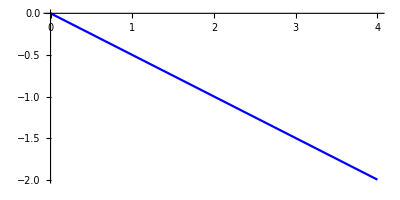

x^3

```mathematica
(*3. Feladat*)
(*EGYSZERŰ GENETIKUS ALGORITMUS*)
initializeGA[fitnessFunction_,{x0_,x1_},{y0_,y1_},divpointCount_:10,eps_:0.1]:=Module[
{it,xx,yy,func,fitness},
it=0;
xx=Table[N[x0+(x1-x0)*i/(divpointCount-1)],{i,0,divpointCount-1}];
yy=Table[N[y0+(y1-y0)*i/(divpointCount-1)],{i,0,divpointCount-1}];
func=Interpolation[Transpose[{xx,yy}]];
fitness=fitnessFunction[func];
{it,xx,yy,divpointCount,func,fitnessFunction,fitness}];

runGA[{it_,xx_,yy_,divpointCount_,func_,fitnessFunction_,fitness_},times_:10,eps_:0.1]:=Module[
{ind,rnd,newyy,newfunc,newfitness,
oldyy=yy,oldfunc=func,oldfitness=fitness},
Do[
ind=RandomInteger[{2,divpointCount-1}];
rnd=RandomReal[{-eps,eps}];
newyy=oldyy;
newyy[[ind]]=newyy[[ind]]+rnd;
newfunc=Interpolation[Transpose[{xx,newyy}]];
newfitness=fitnessFunction[newfunc];
If[newfitness>oldfitness,
oldfitness=newfitness;
oldyy=newyy;
oldfunc=newfunc;
];
,times];
{it+times,xx,oldyy,divpointCount,oldfunc,fitnessFunction,oldfitness}
];

exampleFitnessFunction[fun_]:=
-NIntegrate[exampleF[x,fun[x],fun'[x]],{x,-1,1}]

<<VariationalMethods`
exampleAE=FullSimplify[EulerEquations[exampleF[x,y[x],y'[x]],y[x],x]];
exampleY[x_]=DSolveValue[{exampleAE,y[-1]==-1,y[1]==1},y[x],x] (*ezt kell atirni azt hiszem*)
exmapleOptimalFitness=N[exampleFitnessFunction[exampleY]];
exampleGA=initializeGA[exampleFitnessFunction,{-1,1},{-1,1},10];

Manipulate[
If[run,
exampleGA=runGA[exampleGA];
];
Column[{
"Iteráció:    "<>ToString[exampleGA[[1]]],
"Fitnesz:     "<>ToString[exampleGA[[7]]],
"Opt. Fitnes: "<>ToString[exmapleOptimalFitness],
Show[
examplePlot,
Plot[exampleGA[[5]][t],{t,-1,1}],
ListPlot[Transpose[exampleGA[[2;;3]]]],
ImageSize->Medium
]}]
,"GA szimuláció",
{{run,False},None},Button["Run/Stop GA",run=Not[run]],SaveDefinitions->True]
```